```mathematica
ClearAll["Global`*"]
```

# -Graphics-

```mathematica
j0=11/2;
theta0=70*π/180;
j1=j0*Cos[theta0];
j2=j0*Sin[theta0];
moi1=10;
moi2=40;
moi3=20;
A1Const=1/(2*moi1);
A2Const=1/(2*moi2);
A3Const=1/(2*moi3);
```

```mathematica
x1[I_,theta_,phi_]:=I*Sin[theta]*Sin[phi];
x2[I_,theta_,phi_]:=I*Cos[theta];
x3[I_,theta_,phi_]:=I*Sin[theta]*Cos[phi];
A[I_]:=A2Const*(1-j2/I)-A1Const;
u[I_]:=(A3Const-A1Const)/A[I];
v0[I_]:=(-A1Const*j1)/A[I];
Hprime[I_,theta_,phi_]:=x2[I,theta,phi]^2+u[I]*x3[I,theta,phi]^2+2*v0[I]*x1[I,theta,phi];
```

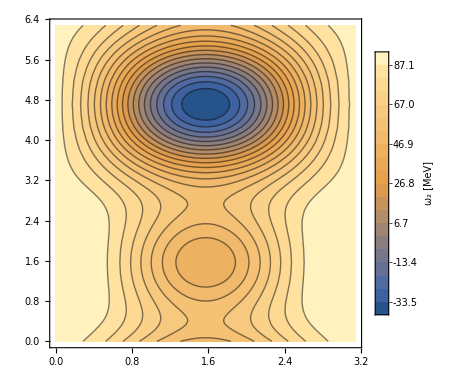

```mathematica
ContourPlot[Hprime[19/2,theta,phi],{theta,0,π},{phi,0,2π},AspectRatio->1,Contours->19,Frame->True,FrameStyle->Directive[Black,Thick],PlotRangePadding->None,LabelStyle->{19,Black,FontFamily->"Latin Modern Roman"},ImageSize->380,PlotLegends->BarLegend[Automatic,19,LegendLabel->"ω_2 [MeV]"]]
```